```mathematica
ClearAll;
```

```mathematica
(*Parameters*)
mu=1.0; (*Solved using constraint on total energy*)
M=1.0;
L=1.0;
z0=0.5;
alpha=0.01; (*Important parameter*)
```

```mathematica
(*Define the logcosh function*)logcosh[x_]:=Module[{s,p},(*Compute s and p similar to Python's np.sign and np.exp*)s=Sign[x]*x;
p=Exp[-2*s];
(*Return the result of the logcosh function*)s+Log[1+p]-Log[2]];

(*Define the H function*)
H[mu_,ics_,alpha_]:=Module[{w,z,phi,pw,pz,pphi,L,M,z0},(*If ics is a 1D array,unpack values accordingly*)If[ArrayDepth[ics]==1,{w,z,phi,pw,pz,pphi}=ics,(*Otherwise,assume it's a 2D array and unpack columns*){w,z,phi,pw,pz,pphi}=Transpose[ics]];
(*Assign constants*)L=pphi;
M=1.;(*Example value,you can replace it if needed*)z0=0.5;(*Example value,you can replace it if needed*)(*Return the result of the Hamiltonian*)mu*(pw^2/(2*mu)+pz^2/(2*mu)+L^2/(2*mu^2*w^2)-M/Sqrt[w^2+z^2]+alpha*z0*logcosh[z/z0])];
```

```mathematica
(*Initialize ics*)
ics={1.2,0.0,0.0,0.0,0.76,L};

(*Initialize t*)
tspan=Range[0,100000,1];
```

```mathematica
(*Define function to evolve the system*)evolve[t_,x_,alpha_]:=Module[{w,z,phi,pw,pz,pphi,dw,dz,dphi,dpw,dpz,dpphi},{w,z,phi,pw,pz,pphi}=x;
(*Calculate derivatives*)
dw=pw;
dz=pz;
dphi=L/(mu*w^2);
dpw=-mu*(-L^2/(mu^2*w^3)+M*w/((w^2+z^2)^(3/2)));
dpz=-mu*(M*z/((w^2+z^2)^(3/2))+alpha*Tanh[z/z0]);
dpphi=0.0;
(*Return result as a list (equivalent to np.array in Python)*){dw,dz,dphi,dpw,dpz,dpphi}];
```

```mathematica
(*Poincare function*)poincare[t_Real,y_List,args_Integer]:=y[[2]]
```

```mathematica
(*Solve the differential equation system*){sol,points}=Reap@NDSolve[{(*System of differential equations*)Thread[D[{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},t]==evolve[t,{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},alpha]],(*Initial conditions*)w[0]==ics[[1]],z[0]==ics[[2]],phi[0]==ics[[3]],pw[0]==ics[[4]],pz[0]==ics[[5]],pphi[0]==ics[[6]],(*Poincare section condition*)WhenEvent[z[t]==0 && pz[t]>0, Sow[{z[t],pz[t]}]]},{w[t],z[t],phi[t],pw[t],pz[t],pphi[t]},{t,0,tspan[[-1]]},Method->{"StiffnessSwitching"},AccuracyGoal->11,PrecisionGoal->11];
```

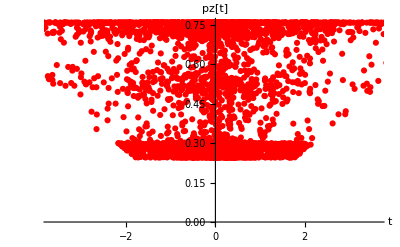

```mathematica
(*Plot the points*)ListPlot[points,PlotStyle->Red,PlotLegends->"Expressions",AxesLabel->{"t","pz[t]"},PlotMarkers->Automatic]
```

```mathematica
points
```